```mathematica
ClearAll
```

ClearAll

# biological parameters

```mathematica
c=299792458 ;hb=1.0545715964207855*10^-34;ϵ0=8.85*10^-12;re=2.82*10^-13*10^-2;
q=1.602*10^-19;
```

```mathematica
wsig=9*10^3*q/hb;
```

```mathematica
λsig=2*Pi*c/wsig;
```

```mathematica
f1C=6.01;f1N=7.02;f1H=1;f1O=8.04;f1S=16.27;f1CI=17.31;
```

```mathematica
AC=12.011;AN=14.007;AH=1.008;AO=15.999;AS=32.06;ACI=35.45;
NA=6.022*10^23;cmCubeToMeterCube=100^3;
```

```mathematica
phase[sH_,sC_,sN_,sO_,sS_,sCI_,thickness_,materialDensity_,λ_]:=((2 π)/λ)*thickness*(re/(2 π))*materialDensity*NA*(1/(sH*AH+sC*AC+sN*AN+sO*AO+sS*AS+sCI*ACI))*(sH*f1H+sC*f1C+sN*f1N+sO*f1O+sS*f1S+sCI*f1CI)*λ^2*cmCubeToMeterCube
```

```mathematica
phase[48.6,32.9,8.9,8.9,0.6,0,5*10^-9,1.35,λsig]
```

0.000843499

# cropping functions

```mathematica
Clear[lowerleft]
lowerleft=Function[biosample,For[i=1,i<0.2*Dimensions[biosample][[1]],i++,For[j=1,j<0.2*Dimensions[biosample][[2]],j++,If[biosample[[i,j]]==0,Break[]]];If[biosample[[i,j]]==0,Break[]]];{i,j}](*{minindex1,minindex2}*);
```

```mathematica
Clear[upperight]
upperight=Function[biosample,For[i=Floor[0.8*Dimensions[biosample][[1]]],i<Dimensions[biosample][[1]],i++,For[j=Floor[0.8*Dimensions[biosample][[2]]],j<Dimensions[biosample][[2]],j++,If[biosample[[i,j]]==1,Break[]]]];{i,j}](*{maxindex1,maxindex2}*);
```

```mathematica
Clear[croping]
croping[biosample_]:=ImageData[ImageTake[Image[biosample],{Dimensions[biosample][[1]]-upperight[biosample][[1]]+1,Dimensions[biosample][[1]]-lowerleft[biosample][[1]]+1},{lowerleft[biosample][[2]],upperight[biosample][[2]]}]]
```

# uploading the biological features and assigning them the biological data

## upload the folded protein pattern

```mathematica
Clear[foldedProtein]
foldedProtein=Import["G:\\Haim\\SU 11 project\\papers\\Imaging\\My paper\\codes\\biological imaging\\biological features\\foldedProtein.JPG"];
```

```mathematica
temp=foldedProtein;
foldedProtein=ImageResize[temp,150](*ImageResize[temp,150]*)
```

-Graphics-

```mathematica
Clear[temp]
temp=foldedProtein;
foldedProtein=ImageData[ColorConvert[temp,"Grayscale"]];
```

```mathematica
Image[foldedProtein]
```

-Graphics-

```mathematica
Clear[temp]
temp=croping[foldedProtein];
Clear[foldedProtein]
foldedProtein=Table[temp[[i,j]],{i,1,Dimensions[temp][[1]]},{j,1,Dimensions[temp][[2]]}];
```

```mathematica
Image[foldedProtein]
```

-Graphics-

## assign corresponding refractive coefficients to the folded protein pattern

```mathematica
Clear[temp]
temp=foldedProtein;
biosample01=temp*phase[48.6,32.9,8.9,8.9,0.6,0,(5*5/2)*10^-9,1.35,λsig];
Image[biosample01]
Image[biosample01/Max[biosample01]]
```

-Graphics-

-Graphics-

```mathematica
(*1. Import,Resize,and Convert to Grayscale*)
ClearAll[foldedProtein];
SetDirectory["G:\\Haim\\SU 11 project\\papers\\Imaging\\My paper\\codes\\biological imaging\\biological features"];

(*Import the image and resize it to 150 pixels width*)
foldedProtein=Import["foldedProtein.JPG"]//ImageResize[#,150]&;

(*Convert to Grayscale and extract numerical ImageData for mathematical processing*)
foldedProteinData=ImageData[ColorConvert[foldedProtein,"Grayscale"]];

(*2. Dimension Checks (if needed for subsequent steps)*)
Print["Dimensions: ",Dimensions[foldedProteinData]];
(*Example:{143,150}*)

(*3. Cropping*)
(*Apply the pre-defined'croping' function and update the main variable*)
foldedProteinData=croping[foldedProteinData];

(*Print["Cropped Dimensions: ",Dimensions[foldedProteinData]];
Image[foldedProteinData] (*Display the cropped image*)
*)
(*4. Create the Bio Sample*)
(*Multiply the image data by the pre-defined'phase' function*)
biosample01=foldedProteinData*phase[48.6,32.9,8.9,8.9,0.6,0,(5*5/2)*10^-9,1.35,λsig];

(*Display the processed sample image*)
Image[biosample01]
(*Display the normalized image for better visualization*)
Image[biosample01/Max[biosample01]]
```

## upload the small protein pattern

```mathematica
Clear[twoSmallProteins]
twoSmallProteins=Import["G:\\Haim\\SU 11 project\\papers\\Imaging\\My paper\\codes\\biological imaging\\biological features\\twoSmallProteins.JPG"];
```

```mathematica
Clear[temp]
temp=twoSmallProteins;
twoSmallProteins=ImageResize[temp,150](*ImageResize[temp,150]*)
```

-Graphics-

```mathematica
Clear[temp]
temp=twoSmallProteins;
twoSmallProteins=ImageData[ColorConvert[temp,"Grayscale"]];
```

```mathematica
Image[twoSmallProteins]
```

-Graphics-

```mathematica
Clear[temp]
temp=croping[twoSmallProteins];
Clear[twoSmallProteins]
twoSmallProteins=Table[temp[[i,j]],{i,1,Dimensions[temp][[1]]},{j,1,Dimensions[temp][[2]]}];
```

```mathematica
Image[twoSmallProteins]
```

-Graphics-

## assign corresponding refractive coefficients to the small protein pattern

```mathematica
Clear[temp]
temp=twoSmallProteins;
biosample02=temp*phase[48.6,32.9,8.9,8.9,0.6,0,(3*5/2)*10^-9,1.35,λsig];
Image[biosample02]
Image[biosample02/Max[biosample02]]
```

-Graphics-

-Graphics-

## upload the large protein pattern

```mathematica
Clear[twoLargeProteins]
twoLargeProteins=Import["G:\\Haim\\SU 11 project\\papers\\Imaging\\My paper\\codes\\biological imaging\\biological features\\twoLargeProteins.JPG"];
```

```mathematica
Clear[temp]
temp=twoLargeProteins;
twoLargeProteins=ImageResize[temp,150](*ImageResize[temp,150]*)
```

-Graphics-

```mathematica
Clear[temp]
temp=twoLargeProteins;
twoLargeProteins=ImageData[ColorConvert[temp,"Grayscale"]];
```

```mathematica
Image[twoLargeProteins]
```

-Graphics-

```mathematica
Clear[temp]
temp=croping[twoLargeProteins];
Clear[twoLargeProteins]
twoLargeProteins=Table[temp[[i,j]],{i,1,Dimensions[temp][[1]]},{j,1,Dimensions[temp][[2]]}];
```

```mathematica
Image[twoLargeProteins]
```

-Graphics-

## assign corresponding refractive coefficients to the large protein pattern

```mathematica
Clear[temp]
temp=twoLargeProteins;
biosample03=temp*phase[48.6,32.9,8.9,8.9,0.6,0,(5*5/2)*10^-9,1.35,λsig];
Image[biosample03]
Image[biosample03/Max[biosample03]]
```

-Graphics-

-Graphics-

## assign corresponding refractive coefficients to the lipid layer

```mathematica
lipid=Table[phase[62.5,31.5,0,6.3,0,0,45*10^-9,1,λsig],{i,1,139},{j,1,144}];
```

```mathematica
Image[lipid]
```

-Graphics-

## assign corresponding refractive coefficients to the lice cube

```mathematica
water=Table[phase[2,0,0,1,0,0,5*10^-6,0.92,λsig],{i,1,139},{j,1,144}];
```

```mathematica
Image[water]
```

-Graphics-

# creating the total biological sample

```mathematica
Clear[totalbiosample]
totalbiosample=biosample01+biosample02+biosample03+lipid(*+water*);
```

```mathematica
Clear[totalbiosample]
totalbiosample=ImageData[%292];
Image[totalbiosample/Max[totalbiosample]]
```

-Graphics-

```mathematica
Image[1-(totalbiosample/Max[totalbiosample])]
```

-Graphics-

```mathematica
Clear[totalimageBG]
totalimageBG=Table[phase[2,0,0,1,0,0,5*10^-6,0.92,λsig],{i,1,Dimensions[totalbiosample][[1]]},{j,1,Dimensions[totalbiosample][[2]]}] (* this is for 5 micron water *);
```

```mathematica
Clear[temp]
temp=totalbiosample;
totalbiosample=temp+totalimageBG;
```

```mathematica
Image[totalbiosample]
```

-Graphics-

```mathematica
totalbiosample
```

{{0.605691,0.605691,0.605691,0.605691,126,0.605691,0.605691,0.605691,0.605691},132,{1}}
 |  |  |  |

```mathematica
Image[totalbiosample/Max[totalbiosample]]
```

-Graphics-

```mathematica
Image[1-(totalbiosample/Max[totalbiosample])]
```

-Graphics-

# creating a matrix for the signal (“S”) angular deviations

## the object pixel size must be smaller than the imaging resolution → (FOV sig)/(minimal resolution) = 10^-6/10^-9 = 10^3 < number of object 1D pixels

```mathematica
σθp0=4.13*10^-6(* σθp should be of the order of 0.77*objXpixel to achieve the Rayleigh limit *);
θp0=-1.1556175944769262;ks=4.559401012488846*^10;kp=4.560414567875652*^10;ki=2.446282748793892*^7;
```

```mathematica
fs=0.003;
```

```mathematica
res=(fs kp σθp0)/(ks*Sec[θp0])
```

4.99866×10^-9

```mathematica
pixelsize=0.5*res (* the smallest separation in my image is 2 pixels than we need to multiply by 0.5 for that separation to correspond to 5 nm *)
```

2.49933×10^-9

```mathematica
angularPixel=0.5*res/fs
```

8.3311×10^-7

```mathematica
2*angularPixel/σθp0
```

0.403443

```mathematica
angularPixel*(Dimensions[totalbiosample][[1]])
```

0.000111637

```mathematica
δsθxmin=-angularPixel*(Dimensions[totalbiosample][[1]])/2
δsθxmax=angularPixel*(Dimensions[totalbiosample][[1]])/2
```

-0.0000558184

0.0000558184

```mathematica
ScientificForm[δsθxmax]
```

5.58184×10^-5

```mathematica
δsθymin=-angularPixel*(Dimensions[totalbiosample][[2]])/2
δsθymax=angularPixel*(Dimensions[totalbiosample][[2]])/2
```

-0.0000558184

0.0000558184

```mathematica
jmax=Dimensions[totalbiosample][[2]];jmin=1;imax=Dimensions[totalbiosample][[2]];imin=1;
```

```mathematica
(δsθxmax-δsθxmin)/(imax-imin+1)
```

8.3311×10^-7

```mathematica
objXpixel=(δsθxmax-δsθxmin)/(imax-imin+1)  (* this should TURN OUT TO BE EQUAL to angularPixel *)
```

8.3311×10^-7

```mathematica
N[objXpixel]
```

8.3311×10^-7

```mathematica
objYpixel=(δsθymax-δsθymin)/(jmax-jmin+1)(* this should TURN OUT TO BE EQUAL to angularPixel *)
```

8.3311×10^-7

```mathematica
N[objYpixel]
```

8.3311×10^-7

```mathematica
δsθx=Range[δsθxmin*0.995,δsθxmax*0.995,objXpixel];
Dimensions[δsθx]
```

{134}

```mathematica
δsθy=Range[δsθymin*0.995,δsθymax*0.995,objYpixel];
Dimensions[δsθy]
```

{134}

```mathematica
N[129*(5*10^-9)/2] (*  this is the FOV of this image in meters *)
```

3.225×10^-7

# creating a matrix for the idelr (“I”) angular deviations

```mathematica
δiθxmin=δsθxmin*ks/ki
δiθxmax=δsθxmax*ks/ki
δiθymin=δsθymin*ks/ki
δiθymax=δsθymax*ks/ki
```

-0.104035

0.104035

-0.104035

0.104035

```mathematica
imageXpixel=(δiθxmax-δiθxmin)/(imax-imin+1)
```

0.00155276

```mathematica
δiθx=Range[δiθxmin*0.995,δiθxmax*0.995,imageXpixel];
Dimensions[δiθx]
```

{134}

```mathematica
imageYpixel=(δiθymax-δiθymin)/(jmax-jmin+1)
```

0.00155276

```mathematica
δiθy=Range[δiθymin*0.995,δiθymax*0.995,imageYpixel];
Dimensions[δiθy]
```

{134}

```mathematica
Dimensions[δiθy][[1]]
```

134

# writing the input pump function

## writing the matrix of the idler angular deviations based on the pump beam width

```mathematica
Clear[func]
func[σθp_,i_,j_,m_,n_]:=(*1/(√(2*π) σθp)**)ⅇ^(-((((ki δiθx[[m]]+ks δsθx[[i]])^2+(ki δiθy[[n]]+ks δsθy[[j]])^2) Sec[θp0]^2)/kp^2)/σθp^2)
```

## writing the matrix of the idler image

## part 1:

```mathematica
(*  nij = (#nPDC per unit area)*(area of the ENTIRE object)  *)
```

```mathematica
Dimensions[δiθy]
```

{134}

```mathematica
Clear[normalization]
normalization[σθp_]:=ParallelTable[Sum[func[σθp,i,j,m,n],{i,1,Dimensions[δsθx][[1]]},{j,1,Dimensions[δsθy][[1]]}],{m,1,Dimensions[δiθx][[1]]},{n,1,Dimensions[δiθy][[1]]}];
```

```mathematica
Clear[sf]
sf[σθp_]:=(1/normalization[σθp])*ParallelTable[Sum[(*2*nPDC/objarea**)Sin[totalbiosample[[i,j]]]*func[σθp,i,j,m,n],{i,1,Dimensions[δsθx][[1]]},{j,1,Dimensions[δsθy][[1]]}],{m,1,Dimensions[δiθx][[1]]},{n,1,Dimensions[δiθy][[1]]}];
```

```mathematica
Image[Abs[1-totalimageBG]]
Image[Abs[totalimageBG]]
Clear[sbg]
sbg[σθp_]:=(1/normalization[σθp])*ParallelTable[Sum[(*2*nPDC/objarea**)Sin[totalimageBG[[i,j]]]*func[σθp,i,j,m,n],{i,1,Dimensions[δsθx][[1]]},{j,1,Dimensions[δsθy][[1]]}],{m,1,Dimensions[δiθx][[1]]},{n,1,Dimensions[δiθy][[1]]}];
```

-Graphics-

-Graphics-

```mathematica
Clear[addΔtotal]
addΔtotal[q_,n1_,objarea_]:=ParallelTable[RandomVariate[NormalDistribution[0,Sqrt[2*(1+q)*n1/objarea]]],{m,1,Dimensions[δiθx][[1]]},{n,1,Dimensions[δiθy][[1]]}](* ⅇ^(-(x-μ)^2/(2 σ^2)), x->Subscript[noise, sf][[m,n]], μ[[m,n]]=0, σ^2=Δ2sf[[m,n]]+Δ2sbg[[m,n]]=2*nPDC/objarea +2*nPDC/objarea*);
```

## part 2:

```mathematica
Clear[Sidler]
Sidler[σθp_]:=sf[σθp]-sbg[σθp];
```

# choosing Region Of Interest (ROI):

```mathematica
SidlerNσθp0=Sidler[σθp0];
```

```mathematica
Image[SidlerNσθp0/Max[Image[SidlerNσθp0]]]
```

-Graphics-

```mathematica
Clear[SidlerROIn]
SidlerROIn[i1_,i2_,j1_,j2_]:=ImageData[ImageTake[Image[SidlerNσθp0(*/Max[SidlerNσθp0]*)],{Dimensions[δiθx][[1]]-i2+1,Dimensions[δiθx][[1]]-i1+1},{Dimensions[δiθy][[1]]-j2+1,Dimensions[δiθy][[1]]-j1+1}]]
```

```mathematica
Clear[addΔtotalROIn]
addΔtotalROIn[q_,n1_,i1_,i2_,j1_,j2_]:=ImageData[ImageTake[Image[addΔtotal[q,n1,1]],{Dimensions[δiθx][[1]]-i2+1,Dimensions[δiθx][[1]]-i1+1},{Dimensions[δiθy][[1]]-j2+1,Dimensions[δiθy][[1]]-j1+1}]]
```

```mathematica
Image[(totalbiosample-totalimageBG)/Max[totalbiosample-totalimageBG]]
```

-Graphics-

```mathematica
Clear[i1Folded, i2Folded,j1Folded, j2Folded,rowMinFolded,rowMaxFolded]
```

```mathematica
rowMinFolded=69;
rowMaxFolded=134;
```

```mathematica
i1Folded=Dimensions[δiθx][[1]]-rowMaxFolded+1
i2Folded=Dimensions[δiθx][[1]]-rowMinFolded+1
j1Folded=24; (* the most left column *)
```

```mathematica
Clear[foldedProteinData]
foldedProteinData=ImageData[ImageTake[Image[(totalbiosample-totalimageBG)],{i1Folded, i2Folded}, {j1Folded, j2Folded}]];
```

```mathematica
Image[foldedProteinData/Max[foldedProteinData]]
```

-Graphics-

# Fourier transforming the folded protein

```mathematica
Clear[SidlerROInFolded]
SidlerROInFolded=SidlerROIn[i1Folded, i2Folded,j1Folded, j2Folded];
```

```mathematica
Clear[qj]
qj=Table[q,{q,{1,5,25}}];
```

```mathematica
Clear[n1]
n1=Table[NPDC,{NPDC,10^5,1*10^8,1.999*10^6}];
```

```mathematica
Clear[a1folded]
a1folded=ParallelTable[Fourier[2*n1[[j]]*Sqrt[qj[[i]]]*SidlerROInFolded+addΔtotalROIn[qj[[i]],n1[[j]],i1Folded, i2Folded,j1Folded, j2Folded],FourierParameters->{1,1}],{i,1,Dimensions[qj][[1]]},{j,1,Dimensions[n1][[1]]}]
```

{1}
 |  |  |  |

```mathematica
a1folded=ParallelTable[RotateRight[a1folded[[i]][[j]],Floor[({Dimensions[foldedProteinData][[2]],Dimensions[foldedProteinData][[1]]}-1)/2]],{i,1,Dimensions[qj][[1]]},{j,1,Dimensions[n1][[1]]}]
```

{1}
 |  |  |  |

```mathematica
Clear[a2folded]
a2folded=ParallelTable[Fourier[2*n1[[j]]*Sqrt[qj[[i]]]*SidlerROInFolded+addΔtotalROIn[qj[[i]],n1[[j]],i1Folded, i2Folded,j1Folded, j2Folded],FourierParameters->{1,1}],{i,1,Dimensions[qj][[1]]},{j,1,Dimensions[n1][[1]]}]
```

{1}
 |  |  |  |

```mathematica
a2folded=ParallelTable[RotateRight[a2folded[[i]][[j]],Floor[({Dimensions[foldedProteinData][[2]],Dimensions[foldedProteinData][[1]]}-1)/2]],{i,1,Dimensions[qj][[1]]},{j,1,Dimensions[n1][[1]]}]
```

1
 |  |  |  |

# creating a search ring filter in the Fourier space

```mathematica
Clear[sign]
sign[i_,j_,min_,max_]:=If[(i-(Floor[Dimensions[foldedProteinData][[1]]/2]))^2+(j-(Floor[Dimensions[foldedProteinData][[2]]/2]))^2≥min^2&&(i-(Floor[Dimensions[foldedProteinData][[2]]/2]))^2+(j-(Floor[Dimensions[foldedProteinData][[2]]/2]))^2≤max^2,1,0]
```

```mathematica
Clear[pp]
pp=Table[0,{i,1,Dimensions[foldedProteinData][[1]]},{j,1,Dimensions[foldedProteinData][[2]]}];

For[i=1,i<=Dimensions[foldedProteinData][[1]],i++,For[j=1,j<=Dimensions[foldedProteinData][[2]],j++,pp[[i,j]]=(*ppp[[i,j]]**)sign[i,j,1,4]]]
```

```mathematica
Image[pp]
```

-Graphics-

```mathematica
Clear[numpix,halfBit]
```

```mathematica
numpix[min_,max_]:=Floor[Pi*(max^2-min^2)];
halfBit[min_,max_]:=(0.2071+1.9102/(√numpix[min,max]))/(1.2071+0.97102/(√numpix[min,max]));
```

```mathematica
halfBitTable=Table[halfBit[min,min+Δr],{min,1,Floor[Dimensions[foldedProteinData][[2]]/2]},{Δr,1,4}];
```

# plotting at different exposures

```mathematica
NPDCs=Table[NPDC,{NPDC,5*10^6,5*10^8,7.07143*10^7}];
```

```mathematica
image1=NPDCs[[1]]*SidlerNσθp0+addΔtotalROIn[NPDCs[[1]],1, Dimensions[SidlerNσθp0][[1]], 1, Dimensions[SidlerNσθp0][[2]]];
Image[image1/Max[image1]]
```

-Graphics-

```mathematica
image4=NPDCs[[4]]*SidlerNσθp0+addΔtotalROIn[NPDCs[[4]],1, Dimensions[SidlerNσθp0][[1]], 1, Dimensions[SidlerNσθp0][[2]]];
Image[image4/Max[image4]]
```

-Graphics-

```mathematica
image7=NPDCs[[7]]*SidlerNσθp0+addΔtotalROIn[NPDCs[[7]],1, Dimensions[SidlerNσθp0][[1]], 1, Dimensions[SidlerNσθp0][[2]]];
Image[image7/Max[image7]]
```

-Graphics-

# showing the ROI image of the the proteins:

```mathematica
Image[SidlerROIn[i1Folded, i2Folded,j1Folded, j2Folded]/Max[SidlerROIn[i1Folded, i2Folded,j1Folded, j2Folded]]]
```

-Graphics-

# FRC of the folded protein:

```mathematica
Clear[p1,p2]
p1={50,29,8};
p2={30,18,5};
```

```mathematica
Clear[Δr]
Δr=3;
```

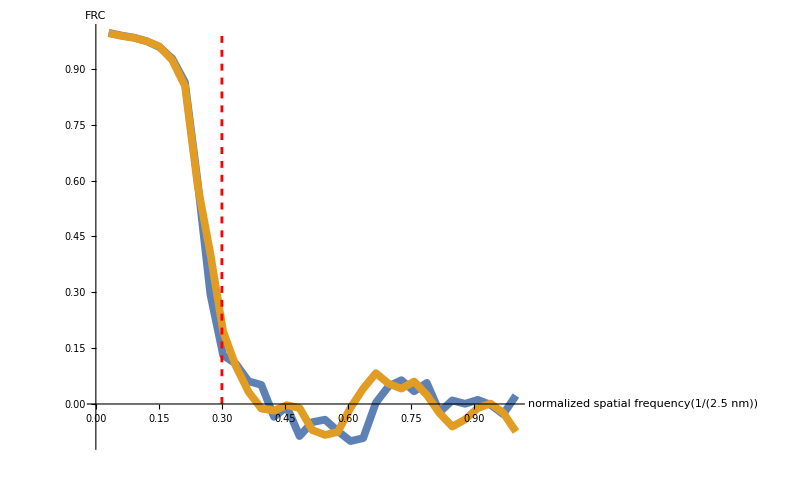
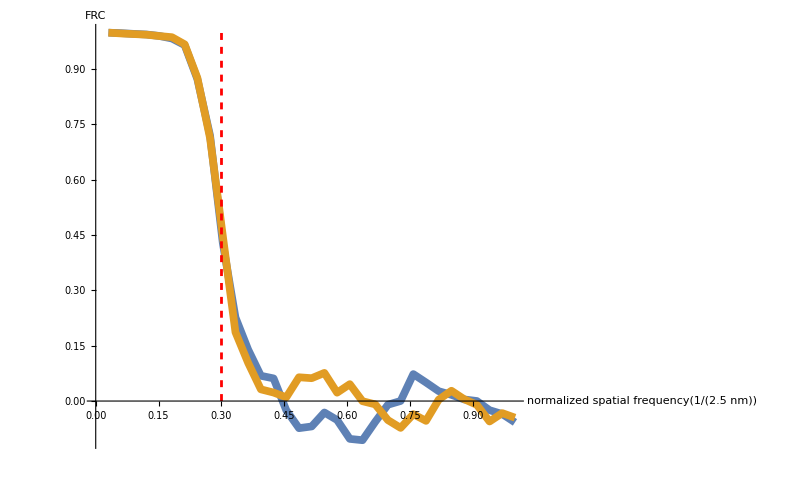
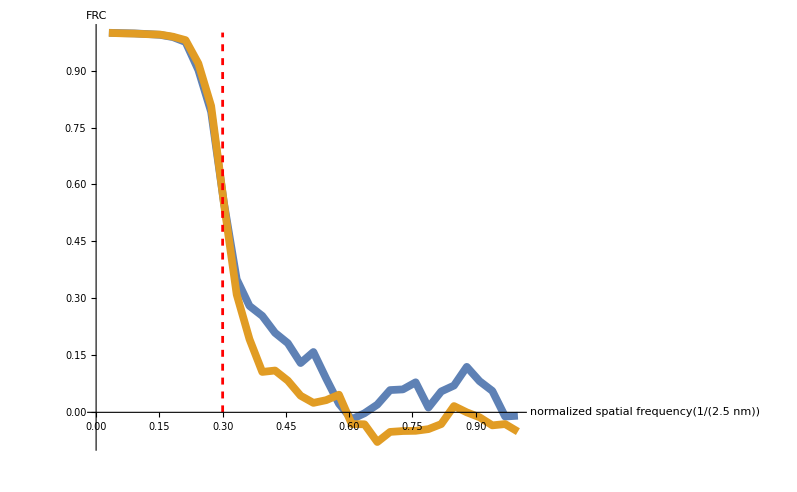

```mathematica
Table[Clear[frcDatan1,frcDatanq];
frcDatan1=ParallelTable[(Sum[Re[a1folded[[1]][[p1[[k1]]]][[i,j]]*Conjugate[a2folded[[1]][[p1[[k1]]]][[i,j]]]*sign[i,j,min,min+Δr]],{i,1,Dimensions[foldedProteinData][[1]]},{j,1,Dimensions[foldedProteinData][[2]]}])/(Sqrt[(Sum[sign[i,j,min,min+Δr]*(Abs[a1folded[[1]][[p1[[k1]]]][[i,j]]])^2,{i,1,Dimensions[foldedProteinData][[1]]},{j,1,Dimensions[foldedProteinData][[2]]}])*(Sum[sign[i,j,min,min+Δr]*(Abs[a2folded[[1]][[p1[[k1]]]][[i,j]]])^2,{i,1,Dimensions[foldedProteinData][[1]]},{j,1,Dimensions[foldedProteinData][[2]]}])]),{min,1,Floor[Dimensions[foldedProteinData][[2]]/2]}];

frcDatanq=ParallelTable[(Sum[Re[a1folded[[2]][[p2[[k2]]]][[i,j]]*Conjugate[a2folded[[2]][[p2[[k2]]]][[i,j]]]*sign[i,j,min,min+Δr]],{i,1,Dimensions[foldedProteinData][[1]]},{j,1,Dimensions[foldedProteinData][[2]]}])/(Sqrt[(Sum[sign[i,j,min,min+Δr]*(Abs[a1folded[[2]][[p2[[k2]]]][[i,j]]])^2,{i,1,Dimensions[foldedProteinData][[1]]},{j,1,Dimensions[foldedProteinData][[2]]}])*(Sum[sign[i,j,min,min+Δr]*(Abs[a2folded[[2]][[p2[[k2]]]][[i,j]]])^2,{i,1,Dimensions[foldedProteinData][[1]]},{j,1,Dimensions[foldedProteinData][[2]]}])]),{min,1,Floor[Dimensions[foldedProteinData][[2]]/2]}];

Show[ListPlot[{Table[{i/(Floor[Dimensions[foldedProteinData][[2]]/2]),frcDatan1[[i]]},{i,1,Floor[Dimensions[foldedProteinData][[2]]/2]}],Table[{i/(Floor[Dimensions[foldedProteinData][[2]]/2]),frcDatanq[[i]]},{i,1,Floor[Dimensions[foldedProteinData][[2]]/2]}]},Joined->True,PlotStyle->Thickness[0.007],LabelStyle->{13,GrayLevel[0],Bold},TicksStyle->Thick],AxesLabel->{HoldForm[normalized spatial frequency[1/(2.5 nm)]],HoldForm[FRC]},PlotLabel->None,LabelStyle->{14,GrayLevel[0],Bold},Epilog->{Dashed,Red,AbsoluteThickness[2],Line[{{0.3,0},{0.3,1}}]}]
,{k1,1,Length[p1]},{k2,1,Length[p2]}]
```

```mathematica
minF
```

{13,14,15,16,18}

```mathematica
bla={1/13,1/14,1/15,1/16,1/18}
```

{1/13,1/14,1/15,1/16,1/18}

```mathematica
bla2=Table[NPDC,{NPDC,30,140,24}]
```

{30,54,78,102,126}

```mathematica
ListPlot[ParallelTable[{bla2[[i]],(5(**10^-9*))/(1/30)*bla[[i]]},{i,1,5}],Joined->True]
```

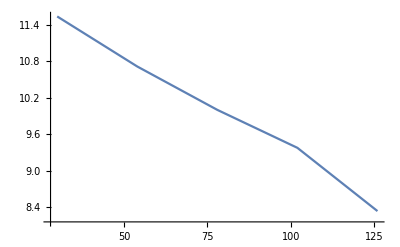

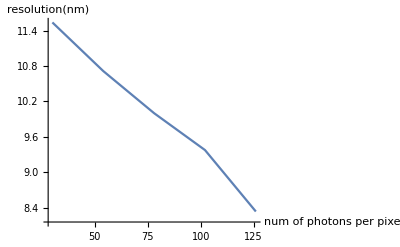

```mathematica
Show[%111,AxesLabel->{HoldForm[num of photons per pixel],HoldForm[resolution[nm]]},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
1/((1/18)*(5)/(1/30))
```

3/25

```mathematica
(1/18)*(5)/(1/30)
```

25/3

```mathematica
N[1/((1/18)*(5)/(1/30))]
```

0.12

```mathematica
0.12*10^9
```

1.2×10^8

```mathematica
N[(1/18)*(5)/(1/30)]
```

8.33333

```mathematica
N[(1/18)*(5*10^-9)/(1/30)]
```

8.33333×10^-9

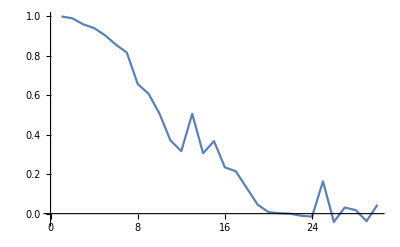

```mathematica
frcMinusBit=Table[(Re[(Sum[a1[[5]][[i,j]]*Conjugate[a2[[5]][[i,j]]]*sign[i,j,min,min+Δr],{i,1,61},{j,1,61}])]/(Sqrt[(Sum[sign[i,j,min,min+Δr]*(Abs[a1[[5]][[i,j]]])^2,{i,1,61},{j,1,61}])*(Sum[sign[i,j,min,min+Δr]*(Abs[a2[[5]][[i,j]]])^2,{i,1,61},{j,1,61}])]))(*-0.5*halfBit[min,min+Δr]*),{min,1,30}];ListPlot[Table[{i,frcMinusBit[[i]]},{i,1,30}],Joined->True]
```